334.507

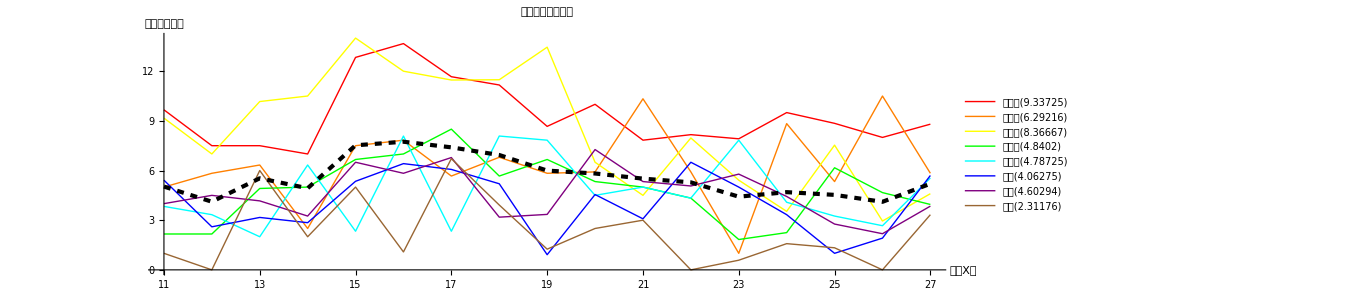

```mathematica
minutes={{580,450,450,420,770,820,700,670,520,600,470,490,475,570,531,480,528},{300,350,380,150,450,470,340,408,350,355,620,355,60,530,320,630,350},{550,420,610,630,840,720,688,689,807,390,270,478,325,212,452,177,276},{130,130,295,300,400,420,510,340,400,320,300,260,110,135,370,280,237},{230,200,120,380,140,485,140,485,470,270,300,260,470,245,195,160,333},{325,156,190,171,321,385,364,312,55,273,185,390,300,200,60,115,342},{240,270,250,195,390,350,407,191,201,436,320,304,347,266,166,131,231},{60,0,360,120,300,65,403,235,75,150,180,0,35,95,80,0,200}};
avebymember=N@(Mean/@minutes)/60;
avebyday=N@(Mean/@(Transpose@minutes));
Mean@avebyday
legends={"王力功","陈周博","徐小博","张碧芸","徐海天","朱成","刘乾","梁栋"};
legends=StringJoin/@Transpose@{legends,("("<>ToString@#<>")"&)/@avebymember};
dates={11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27};
data=(Transpose@({dates,#})&)/@(minutes/60);
Show[
ListLinePlot[data,Ticks->{Range[11,27],Range[0,14]},AxesOrigin->{11,0},ImageSize->1000,AspectRatio->0.3,PlotLegends->legends,InterpolationOrder->1,PlotStyle->(Directive[Thick,#]&)/@{Red,Orange,Yellow,Green,Cyan,Blue,Purple,Brown},AxesLabel->{"五月X日","时长（小时）"},PlotLabel->"全体成员工作时长"],
ListLinePlot[Transpose@({dates,avebyday/60}),PlotStyle->Directive[Thickness@0.003,Black,Dashed]]]
```